```mathematica
BV3to9AllErrors={{{{{{0.8578816641907878,0.06833735104847395,0.06833735104847395,0.005443633712264289},3},{{0.011721749597172097,0.9122757108096575,0.0009641614571841483,0.07503837813598624},4},{{0.011721749597172093,2,20},4},{{0.00016019053753287788,0.01249529310544125,0.012497606039195341,0.9748469103178307},3}},5,{1}}}, {{{, , , , }}}};
```

```mathematica
Populations=BV3to9AllErrors[[;;,;;,1]]
LeadingOrderErrorState=BV3to9AllErrors[[;;,;;,2]];
```

{{{0.857882,0.0683374,0.0683374,0.00544363},{0.0117217,0.912276,0.000964161,0.0750384},{0.0117217,0.000964161,0.912276,0.0750384},{0.000160191,0.0124953,0.0124976,0.974847}},5,{{0.541639,0.043146,0.043146,0.00343693,0.043146,0.00343693,0.00343693,0.00027378,0.043146,0.00343693,0.00343693,0.00027378,0.00343693,0.00027378,0.00027378,227,1.73725×10^-6,1.38387×10^-7,1.73725×10^-6,1.38387×10^-7,1.38387×10^-7,1.10236×10^-8,1.73725×10^-6,1.38387×10^-7,1.38387×10^-7,1.10236×10^-8,1.38387×10^-7,1.10236×10^-8,1.10236×10^-8,8.78123×10^-10},254,{1}}}
 |  |  |  |

```mathematica
Bins=DigitCount[Range[0,2^8-1],2,1]
Length[%]
```

{0,1,1,2,1,2,2,3,1,2,2,3,2,3,3,4,1,2,2,3,2,3,3,4,2,3,3,4,3,4,4,5,1,2,2,3,2,3,3,4,2,3,3,4,3,4,4,5,2,3,3,4,3,4,4,5,3,4,4,5,4,5,5,6,1,2,2,3,2,3,3,4,2,3,3,4,3,4,4,5,2,3,3,4,3,4,4,5,3,4,4,5,4,5,5,6,2,3,3,4,3,4,4,5,3,4,4,5,4,5,5,6,3,4,4,5,4,5,5,6,4,5,5,6,5,6,6,7,1,2,2,3,2,3,3,4,2,3,3,4,3,4,4,5,2,3,3,4,3,4,4,5,3,4,4,5,4,5,5,6,2,3,3,4,3,4,4,5,3,4,4,5,4,5,5,6,3,4,4,5,4,5,5,6,4,5,5,6,5,6,6,7,2,3,3,4,3,4,4,5,3,4,4,5,4,5,5,6,3,4,4,5,4,5,5,6,4,5,5,6,5,6,6,7,3,4,4,5,4,5,5,6,4,5,5,6,5,6,6,7,4,5,5,6,5,6,6,7,5,6,6,7,6,7,7,8}

256

```mathematica
LeadingOrderRatioAllErrs=Table[Table[{j,Diagonal[Populations[[i]]][[j]]/Populations[[i,j]][[LeadingOrderErrorState[[i,j]]]]},{j,1,Length[Populations[[i]]]}],{i,1,Length[Populations]}];
```

```mathematica
LeadingOrderRatioAllErrsBins=Table[Table[{Bins[[i]],Diagonal[Populations[[j]]][[i]]/Populations[[j,i]][[LeadingOrderErrorState[[j,i]]]]},{i,1,Length[Populations[[j]]]}],{j,1,7}];
```

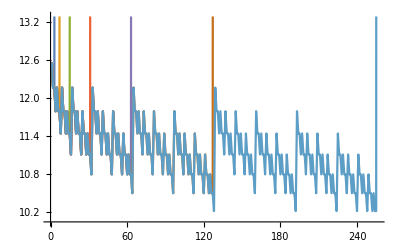

```mathematica
ListLinePlot[LeadingOrderRatioAllErrs]
```

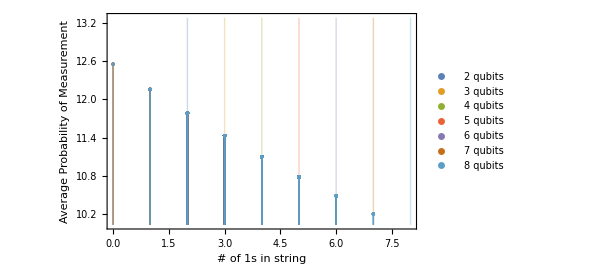

```mathematica
ListPlot[LeadingOrderRatioAllErrsBins,Filling->Bottom,PlotLegends->{"2 qubits","3 qubits","4 qubits", "5 qubits","6 qubits", "7 qubits", "8 qubits" },Frame->True,FrameLabel->{"# of 1s in string","Average Probability of Measurement"}]
```